# Advanced Experimental Physics

## Data Analysis : Electric Transport Properties of Boron-Doped Diamond Sample

## Data import

Example data header
# Channel : Detail 1
# Width : 2.8125 µm
# Height : 2.9297 µm
# Value units : V

```mathematica
units[x_]:= UnitConvert[Quantity[1, "ElementaryCharge"]*Quantity[x,"Volts"],"meV"]
```

```mathematica
bDoped[1]=Map[units,#,{2}]&@-Import["/Users/paul/GitHub/advanced-experimental-physics/Data analysis/scanning probe microscopy/Potential Images/B-Doped SP/Pi1-040825120855.SIG_PI_BKW.FLT"];

Table[bDoped[n]=Map[units,#,{2}]&@-Import["/Users/paul/GitHub/advanced-experimental-physics/Data analysis/scanning probe microscopy/Potential Images/B-Doped SP/Pi"<>ToString[n]<>"-040825121851.SIG_PI_BKW.FLT"],{n,2,8}];

reference[1]=Map[units,#,{2}]&@-Import["/Users/paul/GitHub/advanced-experimental-physics/Data analysis/scanning probe microscopy/Potential Images/Ref SP/Ref1-040825112640.SIG_PI_BKW.FLT"];

reference[2]=Map[units,#,{2}]&@-Import["/Users/paul/GitHub/advanced-experimental-physics/Data analysis/scanning probe microscopy/Potential Images/Ref SP/Ref2-040825113359.SIG_PI_BKW.FLT"];

reference[3]=Map[units,#,{2}]&@-Import["/Users/paul/GitHub/advanced-experimental-physics/Data analysis/scanning probe microscopy/Potential Images/Ref SP/Ref3-040825114342.SIG_PI_BKW.FLT"];
```

## Computations

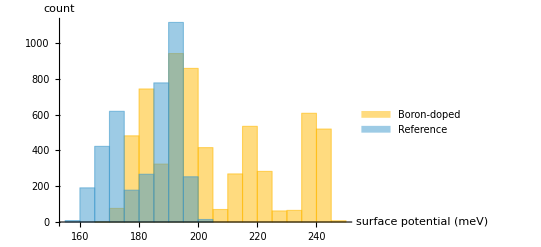

```mathematica
Histogram[{Flatten@Join[Table[bDoped[n],{n,1,8}]],Flatten@Join[Table[reference[n],{n,1,3}]]},AxesLabel->{"surface\npotential (meV)", "count"},ChartLegends->{"Boron-doped","Reference"}]
```

```mathematica
Export["/Users/paul/GitHub/advanced-experimental-physics/Data analysis/scanning probe microscopy/figures/sp_count_bdoped-vs-ref.pdf",];
```

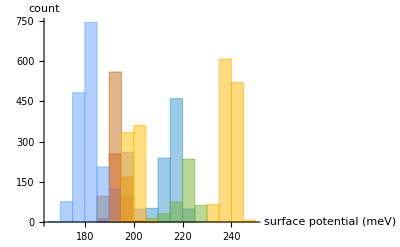

```mathematica
Histogram[Table[Catenate@bDoped[n],{n,1,8}],AxesLabel->{"surface\npotential (meV)", "count"}]
```

```mathematica
Mean@Flatten@Table[
Around[Mean@Flatten@bDoped[i],StandardDeviation@Flatten@bDoped[i]]
-Around[Mean@Flatten@reference[j],StandardDeviation@Flatten@reference[j]]
,{i,1,8},{j,1,3}]
```

(21.91.0) meV

```mathematica
bDopedMean=Around[Mean@#,StandardDeviation@#]&@Flatten@Table[bDoped[i],{i,1,8}]
```

(205.21.) meV

```mathematica
referenceMean=Around[Mean@#,StandardDeviation@#]&@Flatten@Table[reference[i],{i,1,3}]
```

(183.11.) meV

```mathematica
bDopedMean-referenceMean
```

(22.24.) meV